```mathematica
Te=50.0
TI=100.0
data={{0,.0000001,.0000001,.0000001,.0000001},{1,3.500,.0012928910,.0000371464,.0012557450},{2,7.000,.0018069050,.0000519926,.0017549120},{3,10.500,.0021878670,.0000638674,.0021239990},{4,14.000,.0024976590,.0000738880,.0024237700},{5,17.500,.0027607230,.0000826107,.0026781130},{6,21.000,.0029898670,.0000904115,.0028994550},{7,24.500,.0031929620,.0000976689,.0030952930},{8,28.000,.0033750520,.0001044814,.0032705710},{9,31.500,.0035396420,.0001108479,.0034287940},{10,35.000,.0036894420,.0001169162,.0035725260},{11,38.500,.0038263540,.0001226017,.0037037530},{12,42.000,.0039521260,.0001281005,.0038240260},{13,45.500,.0040679840,.0001333770,.0039346070},{14,49.000,.0041749500,.0001384244,.0040365250},{15,52.500,.0042739540,.0001433074,.0041306470},{16,56.000,.0043657350,.0001480304,.0042177050},{17,59.500,.0044509420,.0001526189,.0042983240},{18,63.000,.0045301320,.0001570935,.0043730390},{19,66.500,.0046037720,.0001614381,.0044423340},{20,70.000,.0046722780,.0001656509,.0045066280},{21,73.500,.0047360220,.0001697354,.0045662870},{22,77.000,.0047954280,.0001737825,.0046216460},{23,80.500,.0048507450,.0001777444,.0046730000},{24,84.000,.0049021840,.0001815717,.0047206120},{25,87.500,.0049500850,.0001853526,.0047647320},{26,91.000,.0049946390,.0001890597,.0048055790},{27,94.500,.0050360370,.0001926831,.0048433530},{28,98.000,.0050744780,.0001962389,.0048782390},{29,101.500,.0051101550,.0001997482,.0049104070},{30,105.000,.0051432220,.0002032024,.0049400190},{31,108.500,.0051738130,.0002065997,.0049672140},{32,112.000,.0052020490,.0002099123,.0049921360},{33,115.500,.0052280920,.0002131980,.0050148950},{34,119.000,.0052520400,.0002164270,.0050356130},{35,122.500,.0052740430,.0002196390,.0050544040},{36,126.000,.0052941290,.0002227633,.0050713660},{37,129.500,.0053124500,.0002258569,.0050865930},{38,133.000,.0053290990,.0002289252,.0051001740},{39,136.500,.0053441240,.0002319310,.0051121930},{40,140.000,.0053576500,.0002349215,.0051227290},{41,143.500,.0053697190,.0002378613,.0051318570},{42,147.000,.0053804070,.0002407589,.0051396480},{43,150.500,.0053898030,.0002436371,.0051461650},{44,154.000,.0053979430,.0002464765,.0051514660},{45,157.500,.0054049030,.0002492846,.0051556190},{46,161.000,.0054107300,.0002520534,.0051586770},{47,164.500,.0054154760,.0002547912,.0051606850},{48,168.000,.0054192220,.0002575205,.0051617010},{49,171.500,.0054219620,.0002601883,.0051617730},{50,175.000,.0054238010,.0002628559,.0051609450},{51,178.500,.0054247410,.0002654830,.0051592580},{52,182.000,.0054248310,.0002680814,.0051567500},{53,185.500,.0054241310,.0002706619,.0051534700},{54,189.000,.0054226600,.0002732183,.0051494420},{55,192.500,.0054204560,.0002757463,.0051447100},{56,196.000,.0054175540,.0002782512,.0051393030},{57,199.500,.0054139950,.0002807360,.0051332590},{58,203.000,.0054097770,.0002831841,.0051265930},{59,206.500,.0054049880,.0002856318,.0051193560},{60,210.000,.0053996120,.0002880494,.0051115630},{61,213.500,.0053936820,.0002904368,.0051032450},{62,217.000,.0053872460,.0002928238,.0050944220},{63,220.500,.0053802850,.0002951631,.0050851220},{64,224.000,.0053728690,.0002975038,.0050753660},{65,227.500,.0053650090,.0002998280,.0050651810},{66,231.000,.0053567160,.0003021266,.0050545890},{67,234.500,.0053480070,.0003044048,.0050436030},{68,238.000,.0053389010,.0003066498,.0050322520},{69,241.500,.0053294320,.0003088898,.0050205420},{70,245.000,.0053196210,.0003111270,.0050084950},{71,248.500,.0053094710,.0003133313,.0049961400},{72,252.000,.0052990040,.0003155193,.0049834850},{73,255.500,.0052882270,.0003176936,.0049705330},{74,259.000,.0052771750,.0003198545,.0049573200},{75,262.500,.0052658510,.0003219977,.0049438540},{76,266.000,.0052542730,.0003241284,.0049301450},{77,269.500,.0052424560,.0003262499,.0049162060},{78,273.000,.0052304040,.0003283494,.0049020550},{79,276.500,.0052181230,.0003304228,.0048877000},{80,280.000,.0052056450,.0003324937,.0048731510},{81,283.500,.0051929760,.0003345516,.0048584250},{82,287.000,.0051801270,.0003365958,.0048435310},{83,290.500,.0051671040,.0003386281,.0048284750},{84,294.000,.0051539070,.0003406329,.0048132740},{85,297.500,.0051405720,.0003426366,.0047979350},{86,301.000,.0051270890,.0003446213,.0047824670},{87,304.500,.0051134820,.0003466079,.0047668740},{88,308.000,.0050997460,.0003485719,.0047511740},{89,311.500,.0050858690,.0003505063,.0047353630},{90,315.000,.0050719130,.0003524535,.0047194590},{91,318.500,.0050578430,.0003543778,.0047034650},{92,322.000,.0050436940,.0003563009,.0046873930},{93,325.500,.0050294430,.0003582020,.0046712420},{94,329.000,.0050151100,.0003600837,.0046550260},{95,332.500,.0050007200,.0003619688,.0046387520},{96,336.000,.0049862540,.0003638380,.0046224160},{97,339.500,.0049717310,.0003657006,.0046060300},{98,343.000,.0049571470,.0003675442,.0045896030},{99,346.500,.0049425210,.0003693868,.0045731350},{100,350.000,.0049278510,.0003712105,.0045566400},{101,353.500,.0049131360,.0003730250,.0045401110},{102,357.000,.0048983910,.0003748336,.0045235580},{103,360.500,.0048836290,.0003766351,.0045069940},{104,364.000,.0048688230,.0003784196,.0044904030},{105,367.500,.0048540030,.0003801920,.0044738120},{106,371.000,.0048391690,.0003819578,.0044572120},{107,374.500,.0048243330,.0003837239,.0044406090},{108,378.000,.0048094770,.0003854707,.0044240070},{109,381.500,.0047946240,.0003872170,.0044074070},{110,385.000,.0047797650,.0003889382,.0043908260},{111,388.500,.0047649060,.0003906603,.0043742450},{112,392.000,.0047500580,.0003923739,.0043576840},{113,395.500,.0047352180,.0003940819,.0043411370},{114,399.000,.0047203960,.0003957805,.0043246150},{115,402.500,.0047055860,.0003974674,.0043081190},{116,406.000,.0046907850,.0003991421,.0042916420},{117,409.500,.0046760230,.0004008160,.0042752070},{118,413.000,.0046612650,.0004024780,.0042587870},{119,416.500,.0046465470,.0004041382,.0042424090},{120,420.000,.0046318420,.0004057800,.0042260620},{121,423.500,.0046171740,.0004074186,.0042097550},{122,427.000,.0046025410,.0004090554,.0041934860},{123,430.500,.0045879430,.0004106760,.0041772660},{124,434.000,.0045733830,.0004122999,.0041610830},{125,437.500,.0045588510,.0004139034,.0041449480},{126,441.000,.0045443570,.0004155034,.0041288540},{127,444.500,.0045299230,.0004171029,.0041128200},{128,448.000,.0045155130,.0004186854,.0040968270},{129,451.500,.0045011590,.0004202713,.0040808870},{130,455.000,.0044868500,.0004218462,.0040650040},{131,458.500,.0044725770,.0004234063,.0040491710},{132,462.000,.0044583650,.0004249718,.0040333930},{133,465.500,.0044442020,.0004265257,.0040176760},{134,469.000,.0044300890,.0004280773,.0040020120},{135,472.500,.0044160320,.0004296175,.0039864150},{136,476.000,.0044020170,.0004311471,.0039708700},{137,479.500,.0043880640,.0004326792,.0039553840},{138,483.000,.0043741640,.0004341991,.0039399640},{139,486.500,.0043603300,.0004357265,.0039246030},{140,490.000,.0043465410,.0004372315,.0039093090},{141,493.500,.0043328110,.0004387327,.0038940780},{142,497.000,.0043191420,.0004402324,.0038789100},{143,500.500,.0043055310,.0004417223,.0038638090},{144,504.000,.0042919910,.0004432157,.0038487760},{145,507.500,.0042785080,.0004446985,.0038338090},{146,511.000,.0042650730,.0004461657,.0038189070},{147,514.500,.0042517140,.0004476409,.0038040730},{148,518.000,.0042384100,.0004491062,.0037893040},{149,521.500,.0042251770,.0004505723,.0037746050},{150,525.000,.0042120020,.0004520259,.0037599770},{151,528.500,.0041988880,.0004534723,.0037454150},{152,532.000,.0041858410,.0004549150,.0037309260},{153,535.500,.0041728570,.0004563508,.0037165060},{154,539.000,.0041599400,.0004577869,.0037021530},{155,542.500,.0041470920,.0004592165,.0036878760},{156,546.000,.0041343030,.0004606412,.0036736620},{157,549.500,.0041215790,.0004620556,.0036595240},{158,553.000,.0041089290,.0004634720,.0036454570},{159,556.500,.0040963390,.0004648846,.0036314550},{160,560.000,.0040838220,.0004662914,.0036175300},{161,563.500,.0040713740,.0004676969,.0036036770},{162,567.000,.0040589740,.0004690849,.0035898890},{163,570.500,.0040466540,.0004704762,.0035761780},{164,574.000,.0040344040,.0004718679,.0035625360},{165,577.500,.0040222150,.0004732472,.0035489680},{166,581.000,.0040100970,.0004746300,.0035354680},{167,584.500,.0039980370,.0004759955,.0035220420},{168,588.000,.0039860510,.0004773646,.0035086860},{169,591.500,.0039741390,.0004787379,.0034954010},{170,595.000,.0039622790,.0004800956,.0034821830},{171,598.500,.0039505000,.0004814569,.0034690430},{172,602.000,.0039387810,.0004828088,.0034559730},{173,605.500,.0039271280,.0004841547,.0034429730},{174,609.000,.0039155460,.0004855040,.0034300420},{175,612.500,.0039040230,.0004868433,.0034171800},{176,616.000,.0038925780,.0004881843,.0034043940},{177,619.500,.0038811930,.0004895151,.0033916770},{178,623.000,.0038698670,.0004908413,.0033790250},{179,626.500,.0038586240,.0004921757,.0033664480},{180,630.000,.0038474330,.0004934968,.0033539370},{181,633.500,.0038363160,.0004948165,.0033414990},{182,637.000,.0038252540,.0004961270,.0033291270},{183,640.500,.0038142670,.0004974409,.0033168270},{184,644.000,.0038033450,.0004987546,.0033045910},{185,647.500,.0037924910,.0005000595,.0032924320},{186,651.000,.0037816960,.0005013620,.0032803340},{187,654.500,.0037709710,.0005026619,.0032683090},{188,658.000,.0037603030,.0005039513,.0032563510},{189,661.500,.0037497090,.0005052487,.0032444600},{190,665.000,.0037391690,.0005065356,.0032326330},{191,668.500,.0037287020,.0005078239,.0032208780},{192,672.000,.0037182950,.0005091068,.0032091880},{193,675.500,.0037079400,.0005103775,.0031975630},{194,679.000,.0036976700,.0005116620,.0031860080},{195,682.500,.0036874440,.0005129310,.0031745130},{196,686.000,.0036772940,.0005142043,.0031630900},{197,689.500,.0036672000,.0005154708,.0031517290},{198,693.000,.0036571690,.0005167364,.0031404330},{199,696.500,.0036472000,.0005179952,.0031292050},{200,700.000,.0036372900,.0005192513,.0031180380},{201,703.500,.0036274450,.0005205114,.0031069340},{202,707.000,.0036176590,.0005217618,.0030958970},{203,710.500,.0036079380,.0005230138,.0030849240},{204,714.000,.0035982710,.0005242608,.0030740100},{205,717.500,.0035886610,.0005255014,.0030631600},{206,721.000,.0035791240,.0005267459,.0030523780},{207,724.500,.0035696330,.0005279834,.0030416500},{208,728.000,.0035602080,.0005292216,.0030309870},{209,731.500,.0035508460,.0005304548,.0030203910},{210,735.000,.0035415350,.0005316837,.0030098510},{211,738.500,.0035322870,.0005329149,.0029993720},{212,742.000,.0035230890,.0005341385,.0029889510},{213,745.500,.0035139520,.0005353623,.0029785900},{214,749.000,.0035048800,.0005365831,.0029682960},{215,752.500,.0034958580,.0005378018,.0029580560},{216,756.000,.0034868970,.0005390197,.0029478770},{217,759.500,.0034779870,.0005402314,.0029377560},{218,763.000,.0034691400,.0005414484,.0029276910},{219,766.500,.0034603360,.0005426495,.0029176860},{220,770.000,.0034515970,.0005438593,.0029077380},{221,773.500,.0034429100,.0005450618,.0028978480},{222,777.000,.0034342770,.0005462610,.0028880160},{223,780.500,.0034257020,.0005474645,.0028782380},{224,784.000,.0034171840,.0005486600,.0028685240},{225,787.500,.0034087070,.0005498523,.0028588550},{226,791.000,.0034002960,.0005510459,.0028492500},{227,794.500,.0033919340,.0005522369,.0028396970},{228,798.000,.0033836300,.0005534298,.0028302010},{229,801.500,.0033753660,.0005546120,.0028207540},{230,805.000,.0033671580,.0005557914,.0028113660},{231,808.500,.0033590120,.0005569795,.0028020320},{232,812.000,.0033509070,.0005581545,.0027927530},{233,815.500,.0033428660,.0005593407,.0027835250},{234,819.000,.0033348600,.0005605121,.0027743480},{235,822.500,.0033269050,.0005616816,.0027652230},{236,826.000,.0033190120,.0005628564,.0027561550},{237,829.500,.0033111640,.0005640241,.0027471400},{238,833.000,.0033033660,.0005651957,.0027381700},{239,836.500,.0032956080,.0005663579,.0027292500},{240,840.000,.0032879070,.0005675196,.0027203870},{241,843.500,.0032802570,.0005686828,.0027115740},{242,847.000,.0032726510,.0005698407,.0027028100},{243,850.500,.0032650970,.0005710016,.0026940950},{244,854.000,.0032575860,.0005721551,.0026854310},{245,857.500,.0032501280,.0005733105,.0026768170},{246,861.000,.0032427090,.0005744597,.0026682490},{247,864.500,.0032353360,.0005756074,.0026597290},{248,868.000,.0032280220,.0005767625,.0026512600},{249,871.500,.0032207500,.0005779078,.0026428420},{250,875.000,.0032135160,.0005790531,.0026344620},{251,878.500,.0032063280,.0005801908,.0026261370},{252,882.000,.0031991880,.0005813292,.0026178580},{253,885.500,.0031920960,.0005824743,.0026096220},{254,889.000,.0031850460,.0005836076,.0026014380},{255,892.500,.0031780400,.0005847435,.0025932970},{256,896.000,.0031710760,.0005858777,.0025851980},{257,899.500,.0031641580,.0005870076,.0025771500},{258,903.000,.0031572850,.0005881399,.0025691450},{259,906.500,.0031504550,.0005892682,.0025611860},{260,910.000,.0031436680,.0005903980,.0025532700},{261,913.500,.0031369170,.0005915195,.0025453970},{262,917.000,.0031302150,.0005926430,.0025375720},{263,920.500,.0031235580,.0005937673,.0025297910},{264,924.000,.0031169350,.0005948864,.0025220480},{265,927.500,.0031103560,.0005960060,.0025143500},{266,931.000,.0031038130,.0005971182,.0025066940},{267,934.500,.0030973160,.0005982359,.0024990800},{268,938.000,.0030908630,.0005993497,.0024915140},{269,941.500,.0030844420,.0006004598,.0024839820},{270,945.000,.0030780690,.0006015734,.0024764950},{271,948.500,.0030717290,.0006026784,.0024690500},{272,952.000,.0030654260,.0006037841,.0024616420},{273,955.500,.0030591710,.0006048937,.0024542770},{274,959.000,.0030529530,.0006059959,.0024469570},{275,962.500,.0030467700,.0006070963,.0024396740},{276,966.000,.0030406270,.0006081981,.0024324290},{277,969.500,.0030345200,.0006092948,.0024252250},{278,973.000,.0030284550,.0006103956,.0024180590},{279,976.500,.0030224250,.0006114915,.0024109330},{280,980.000,.0030164370,.0006125893,.0024038480},{281,983.500,.0030104770,.0006136776,.0023967990},{282,987.000,.0030045550,.0006147678,.0023897870},{283,990.500,.0029986790,.0006158644,.0023828140},{284,994.000,.0029928310,.0006169502,.0023758810},{285,997.500,.0029870200,.0006180382,.0023689820},{286,1001.000,.0029812380,.0006191203,.0023621170},{287,1004.500,.0029755010,.0006202031,.0023552980},{288,1008.000,.0029698000,.0006212898,.0023485110},{289,1011.500,.0029641280,.0006223670,.0023417610},{290,1015.000,.0029584990,.0006234516,.0023350470},{291,1018.500,.0029528960,.0006245274,.0023283680},{292,1022.000,.0029473270,.0006256009,.0023217260},{293,1025.500,.0029417980,.0006266808,.0023151180},{294,1029.000,.0029362990,.0006277538,.0023085450},{295,1032.500,.0029308370,.0006288271,.0023020100},{296,1036.000,.0029254050,.0006298994,.0022955050},{297,1039.500,.0029200040,.0006309663,.0022890370},{298,1043.000,.0029146400,.0006320362,.0022826040},{299,1046.500,.0029093040,.0006331016,.0022762030},{300,1050.000,.0029040030,.0006341668,.0022698370},{301,1053.500,.0028987350,.0006352318,.0022635030},{302,1057.000,.0028935020,.0006362976,.0022572040},{303,1060.500,.0028882920,.0006373565,.0022509360},{304,1064.000,.0028831220,.0006384174,.0022447050},{305,1067.500,.0028779810,.0006394773,.0022385040},{306,1071.000,.0028728680,.0006405339,.0022323350},{307,1074.500,.0028677850,.0006415890,.0022261960},{308,1078.000,.0028627360,.0006426442,.0022200910},{309,1081.500,.0028577130,.0006436956,.0022140170},{310,1085.000,.0028527250,.0006447479,.0022079780},{311,1088.500,.0028477660,.0006458015,.0022019650},{312,1092.000,.0028428420,.0006468546,.0021959880},{313,1095.500,.0028379370,.0006478990,.0021900380},{314,1099.000,.0028330630,.0006489440,.0021841180},{315,1102.500,.0028282220,.0006499909,.0021782310},{316,1106.000,.0028234090,.0006510354,.0021723740},{317,1109.500,.0028186270,.0006520801,.0021665470},{318,1113.000,.0028138680,.0006531192,.0021607490},{319,1116.500,.0028091410,.0006541597,.0021549810},{320,1120.000,.0028044400,.0006551982,.0021492410},{321,1123.500,.0027997700,.0006562366,.0021435340},{322,1127.000,.0027951300,.0006572749,.0021378550},{323,1130.500,.0027905080,.0006583075,.0021322000},{324,1134.000,.0027859170,.0006593384,.0021265790},{325,1137.500,.0027813550,.0006603746,.0021209800},{326,1141.000,.0027768190,.0006614061,.0021154130},{327,1144.500,.0027723130,.0006624387,.0021098740},{328,1148.000,.0027678290,.0006634654,.0021043640},{329,1151.500,.0027633700,.0006644917,.0020988790},{330,1155.000,.0027589420,.0006655205,.0020934220},{331,1158.500,.0027545390,.0006665441,.0020879950},{332,1162.000,.0027501620,.0006675700,.0020825920},{333,1165.500,.0027458090,.0006685934,.0020772150},{334,1169.000,.0027414820,.0006696117,.0020718710},{335,1172.500,.0027371790,.0006706315,.0020665480},{336,1176.000,.0027329060,.0006716512,.0020612550},{337,1179.500,.0027286580,.0006726727,.0020559860},{338,1183.000,.0027244290,.0006736903,.0020507390},{339,1186.500,.0027202270,.0006747037,.0020455230},{340,1190.000,.0027160470,.0006757155,.0020403310},{341,1193.500,.0027118940,.0006767305,.0020351640},{342,1197.000,.0027077690,.0006777438,.0020300250},{343,1200.500,.0027036600,.0006787544,.0020249050},{344,1204.000,.0026995770,.0006797625,.0020198150},{345,1207.500,.0026955210,.0006807700,.0020147510},{346,1211.000,.0026914850,.0006817760,.0020097090},{347,1214.500,.0026874790,.0006827867,.0020046930},{348,1218.000,.0026834870,.0006837901,.0019996970},{349,1221.500,.0026795220,.0006847906,.0019947320},{350,1225.000,.0026755780,.0006857951,.0019897830},{351,1228.500,.0026716610,.0006867956,.0019848650},{352,1232.000,.0026677640,.0006877992,.0019799650},{353,1235.500,.0026638890,.0006887972,.0019750920},{354,1239.000,.0026600370,.0006897952,.0019702410},{355,1242.500,.0026562030,.0006907917,.0019654120},{356,1246.000,.0026523930,.0006917832,.0019606100},{357,1249.500,.0026486100,.0006927828,.0019558270},{358,1253.000,.0026448450,.0006937769,.0019510680},{359,1256.500,.0026411000,.0006947689,.0019463320},{360,1260.000,.0026373740,.0006957581,.0019416160},{361,1263.500,.0026336720,.0006967466,.0019369250},{362,1267.000,.0026299910,.0006977365,.0019322540},{363,1270.500,.0026263330,.0006987255,.0019276070},{364,1274.000,.0026226950,.0006997098,.0019229850},{365,1277.500,.0026190730,.0007006940,.0019183790},{366,1281.000,.0026154750,.0007016791,.0019137960},{367,1284.500,.0026119000,.0007026651,.0019092340},{368,1288.000,.0026083430,.0007036485,.0019046950},{369,1291.500,.0026048050,.0007046281,.0019001770},{370,1295.000,.0026012860,.0007056088,.0018956770},{371,1298.500,.0025977860,.0007065850,.0018912010},{372,1302.000,.0025943120,.0007075650,.0018867470},{373,1305.500,.0025908500,.0007085396,.0018823100},{374,1309.000,.0025874130,.0007095161,.0018778970},{375,1312.500,.0025839920,.0007104907,.0018735010},{376,1316.000,.0025805880,.0007114615,.0018691260},{377,1319.500,.0025772080,.0007124354,.0018647730},{378,1323.000,.0025738420,.0007134078,.0018604340},{379,1326.500,.0025705020,.0007143798,.0018561220},{380,1330.000,.0025671720,.0007153466,.0018518260},{381,1333.500,.0025638630,.0007163124,.0018475510},{382,1337.000,.0025605760,.0007172835,.0018432930},{383,1340.500,.0025573070,.0007182486,.0018390590},{384,1344.000,.0025540560,.0007192153,.0018348410},{385,1347.500,.0025508220,.0007201778,.0018306440},{386,1351.000,.0025476060,.0007211428,.0018264640},{387,1354.500,.0025444030,.0007221025,.0018223010},{388,1358.000,.0025412210,.0007230632,.0018181580},{389,1361.500,.0025380590,.0007240240,.0018140350},{390,1365.000,.0025349110,.0007249812,.0018099300},{391,1368.500,.0025317790,.0007259359,.0018058430},{392,1372.000,.0025286660,.0007268920,.0018017740},{393,1375.500,.0025255720,.0007278497,.0017977220},{394,1379.000,.0025224940,.0007288043,.0017936900},{395,1382.500,.0025194300,.0007297560,.0017896740},{396,1386.000,.0025163910,.0007307113,.0017856800},{397,1389.500,.0025133610,.0007316647,.0017816970},{398,1393.000,.0025103500,.0007326129,.0017777370},{399,1396.500,.0025073560,.0007335630,.0017737930},{400,1400.000,.0025043800,.0007345122,.0017698680},{401,1403.500,.0025014110,.0007354558,.0017659550},{402,1407.000,.0024984680,.0007364049,.0017620630},{403,1410.500,.0024955370,.0007373490,.0017581890},{404,1414.000,.0024926220,.0007382932,.0017543290},{405,1417.500,.0024897220,.0007392360,.0017504860},{406,1421.000,.0024868400,.0007401782,.0017466620},{407,1424.500,.0024839730,.0007411215,.0017428510},{408,1428.000,.0024811190,.0007420602,.0017390590},{409,1431.500,.0024782840,.0007430004,.0017352830},{410,1435.000,.0024754640,.0007439379,.0017315260},{411,1438.500,.0024726590,.0007448788,.0017277800},{412,1442.000,.0024698670,.0007458131,.0017240530},{413,1445.500,.0024670890,.0007467479,.0017203410},{414,1449.000,.0024643270,.0007476812,.0017166460},{415,1452.500,.0024615840,.0007486161,.0017129680},{416,1456.000,.0024588510,.0007495484,.0017093020},{417,1459.500,.0024561300,.0007504795,.0017056510},{418,1463.000,.0024534300,.0007514107,.0017020190},{419,1466.500,.0024507410,.0007523394,.0016984020},{420,1470.000,.0024480620,.0007532655,.0016947960},{421,1473.500,.0024454050,.0007541945,.0016912100},{422,1477.000,.0024427600,.0007551206,.0016876390},{423,1480.500,.0024401300,.0007560479,.0016840820},{424,1484.000,.0024375120,.0007569704,.0016805420},{425,1487.500,.0024349100,.0007578961,.0016770140},{426,1491.000,.0024323210,.0007588197,.0016735010},{427,1494.500,.0024297450,.0007597415,.0016700030},{428,1498.000,.0024271800,.0007606614,.0016665190},{429,1501.500,.0024246320,.0007615811,.0016630500},{430,1505.000,.0024220940,.0007624984,.0016595950},{431,1508.500,.0024195740,.0007634182,.0016561560},{432,1512.000,.0024170670,.0007643364,.0016527310},{433,1515.500,.0024145680,.0007652505,.0016493180},{434,1519.000,.0024120870,.0007661642,.0016459230},{435,1522.500,.0024096160,.0007670773,.0016425390},{436,1526.000,.0024071630,.0007679970,.0016391660},{437,1529.500,.0024047190,.0007689079,.0016358110},{438,1533.000,.0024022870,.0007698181,.0016324690},{439,1536.500,.0023998690,.0007707289,.0016291400},{440,1540.000,.0023974620,.0007716368,.0016258240},{441,1543.500,.0023950760,.0007725513,.0016225240},{442,1547.000,.0023926920,.0007734556,.0016192370},{443,1550.500,.0023903260,.0007743638,.0016159620},{444,1554.000,.0023879670,.0007752686,.0016126980},{445,1557.500,.0023856240,.0007761722,.0016094520},{446,1561.000,.0023832970,.0007770804,.0016062170},{447,1564.500,.0023809740,.0007779800,.0016029940},{448,1568.000,.0023786660,.0007788815,.0015997850},{449,1571.500,.0023763710,.0007797839,.0015965870},{450,1575.000,.0023740900,.0007806856,.0015934040},{451,1578.500,.0023718220,.0007815883,.0015902340},{452,1582.000,.0023695600,.0007824849,.0015870750},{453,1585.500,.0023673110,.0007833818,.0015839290},{454,1589.000,.0023650750,.0007842787,.0015807960},{455,1592.500,.0023628490,.0007851730,.0015776760},{456,1596.000,.0023606390,.0007860719,.0015745670},{457,1599.500,.0023584360,.0007869649,.0015714710},{458,1603.000,.0023562440,.0007878584,.0015683860},{459,1606.500,.0023540650,.0007887507,.0015653150},{460,1610.000,.0023518980,.0007896427,.0015622550},{461,1613.500,.0023497440,.0007905372,.0015592070},{462,1617.000,.0023475940,.0007914242,.0015561700},{463,1620.500,.0023454600,.0007923132,.0015531470},{464,1624.000,.0023433360,.0007932000,.0015501360},{465,1627.500,.0023412210,.0007940845,.0015471370},{466,1631.000,.0023391200,.0007949733,.0015441460},{467,1634.500,.0023370280,.0007958591,.0015411690},{468,1638.000,.0023349490,.0007967446,.0015382040},{469,1641.500,.0023328780,.0007976283,.0015352500},{470,1645.000,.0023308170,.0007985095,.0015323070},{471,1648.500,.0023287720,.0007993973,.0015293750},{472,1652.000,.0023267280,.0008002754,.0015264520},{473,1655.500,.0023247040,.0008011568,.0015235470},{474,1659.000,.0023226830,.0008020336,.0015206490},{475,1662.500,.0023206720,.0008029104,.0015177610},{476,1666.000,.0023186780,.0008037926,.0015148860},{477,1669.500,.0023166900,.0008046696,.0015120210},{478,1673.000,.0023147120,.0008055446,.0015091670},{479,1676.500,.0023127440,.0008064197,.0015063240},{480,1680.000,.0023107870,.0008072960,.0015034910},{481,1683.500,.0023088390,.0008081701,.0015006700},{482,1687.000,.0023069010,.0008090410,.0014978600},{483,1690.500,.0023049720,.0008099124,.0014950600},{484,1694.000,.0023030520,.0008107821,.0014922700},{485,1697.500,.0023011430,.0008116529,.0014894900},{486,1701.000,.0022992480,.0008125270,.0014867210},{487,1704.500,.0022973570,.0008133940,.0014839630},{488,1708.000,.0022954780,.0008142621,.0014812160},{489,1711.500,.0022936050,.0008151287,.0014784770},{490,1715.000,.0022917430,.0008159946,.0014757490},{491,1718.500,.0022898920,.0008168590,.0014730330},{492,1722.000,.0022880470,.0008177225,.0014703250},{493,1725.500,.0022862160,.0008185876,.0014676280},{494,1729.000,.0022843910,.0008194506,.0014649410},{495,1732.500,.0022825750,.0008203126,.0014622620},{496,1736.000,.0022807710,.0008211752,.0014595960},{497,1739.500,.0022789730,.0008220345,.0014569380},{498,1743.000,.0022771860,.0008228961,.0014542900},{499,1746.500,.0022754060,.0008237552,.0014516510},{500,1750.000,.0022736360,.0008246133,.0014490230},{501,1753.500,.0022718750,.0008254705,.0014464040},{502,1757.000,.0022701200,.0008263264,.0014437940},{503,1760.500,.0022683740,.0008271810,.0014411930},{504,1764.000,.0022666380,.0008280351,.0014386030},{505,1767.500,.0022649110,.0008288894,.0014360220},{506,1771.000,.0022631950,.0008297451,.0014334500},{507,1774.500,.0022614850,.0008305956,.0014308890},{508,1778.000,.0022597860,.0008314506,.0014283350},{509,1781.500,.0022580880,.0008322980,.0014257900},{510,1785.000,.0022564060,.0008331491,.0014232570},{511,1788.500,.0022547300,.0008339999,.0014207300},{512,1792.000,.0022530610,.0008348473,.0014182140},{513,1795.500,.0022513970,.0008356948,.0014157020},{514,1799.000,.0022497500,.0008365426,.0014132080},{515,1802.500,.0022481050,.0008373879,.0014107170},{516,1806.000,.0022464730,.0008382367,.0014082370},{517,1809.500,.0022448420,.0008390781,.0014057640},{518,1813.000,.0022432230,.0008399241,.0014032990},{519,1816.500,.0022416110,.0008407638,.0014008470},{520,1820.000,.0022400060,.0008416082,.0013983980},{521,1823.500,.0022384140,.0008424520,.0013959620},{522,1827.000,.0022368250,.0008432921,.0013935330},{523,1830.500,.0022352460,.0008441332,.0013911130},{524,1834.000,.0022336710,.0008449689,.0013887030},{525,1837.500,.0022321070,.0008458096,.0013862980},{526,1841.000,.0022305520,.0008466490,.0013839030},{527,1844.500,.0022290000,.0008474836,.0013815160},{528,1848.000,.0022274610,.0008483216,.0013791390},{529,1851.500,.0022259250,.0008491557,.0013767690},{530,1855.000,.0022244010,.0008499930,.0013744080},{531,1858.500,.0022228780,.0008508257,.0013720530},{532,1862.000,.0022213650,.0008516574,.0013697080},{533,1865.500,.0022198630,.0008524911,.0013673720},{534,1869.000,.0022183650,.0008533230,.0013650420},{535,1872.500,.0022168780,.0008541571,.0013627200},{536,1876.000,.0022153920,.0008549844,.0013604070},{537,1879.500,.0022139140,.0008558119,.0013581030},{538,1883.000,.0022124500,.0008566434,.0013558060},{539,1886.500,.0022109870,.0008574706,.0013535160},{540,1890.000,.0022095350,.0008582996,.0013512350},{541,1893.500,.0022080890,.0008591271,.0013489620},{542,1897.000,.0022066480,.0008599513,.0013466970},{543,1900.500,.0022052150,.0008607789,.0013444370},{544,1904.000,.0022037880,.0008616013,.0013421870},{545,1907.500,.0022023720,.0008624285,.0013399440},{546,1911.000,.0022009570,.0008632488,.0013377080},{547,1914.500,.0021995490,.0008640693,.0013354800},{548,1918.000,.0021981520,.0008648938,.0013332590},{549,1921.500,.0021967580,.0008657120,.0013310460},{550,1925.000,.0021953770,.0008665349,.0013288420},{551,1928.500,.0021939990,.0008673559,.0013266430},{552,1932.000,.0021926240,.0008681718,.0013244520},{553,1935.500,.0021912580,.0008689894,.0013222690},{554,1939.000,.0021899010,.0008698071,.0013200940},{555,1942.500,.0021885510,.0008706275,.0013179230},{556,1946.000,.0021872050,.0008714432,.0013157620},{557,1949.500,.0021858660,.0008722544,.0013136110},{558,1953.000,.0021845330,.0008730703,.0013114620},{559,1956.500,.0021832050,.0008738825,.0013093230},{560,1960.000,.0021818900,.0008747013,.0013071890},{561,1963.500,.0021805750,.0008755119,.0013050630},{562,1967.000,.0021792690,.0008763236,.0013029450},{563,1970.500,.0021779640,.0008771318,.0013008320},{564,1974.000,.0021766680,.0008779413,.0012987270},{565,1977.500,.0021753830,.0008787535,.0012966290},{566,1981.000,.0021741000,.0008795630,.0012945370},{567,1984.500,.0021728240,.0008803707,.0012924530},{568,1988.000,.0021715530,.0008811774,.0012903760},{569,1991.500,.0021702900,.0008819838,.0012883060},{570,1995.000,.0021690340,.0008827937,.0012862400},{571,1998.500,.0021677820,.0008835973,.0012841840},{572,2002.000,.0021665350,.0008844017,.0012821330},{573,2005.500,.0021652950,.0008852060,.0012800890},{574,2009.000,.0021640580,.0008860074,.0012780500},{575,2012.500,.0021628330,.0008868129,.0012760200},{576,2016.000,.0021616100,.0008876147,.0012739960},{577,2019.500,.0021603950,.0008884154,.0012719790},{578,2023.000,.0021591830,.0008892157,.0012699670},{579,2026.500,.0021579760,.0008900138,.0012679620},{580,2030.000,.0021567810,.0008908166,.0012659640},{581,2033.500,.0021555860,.0008916128,.0012639730},{582,2037.000,.0021544010,.0008924135,.0012619870},{583,2040.500,.0021532200,.0008932117,.0012600080},{584,2044.000,.0021520390,.0008940047,.0012580340},{585,2047.500,.0021508710,.0008948041,.0012560670},{586,2051.000,.0021497070,.0008955997,.0012541070},{587,2054.500,.0021485480,.0008963957,.0012521520},{588,2058.000,.0021473920,.0008971865,.0012502050},{589,2061.500,.0021462450,.0008979816,.0012482640},{590,2065.000,.0021450990,.0008987722,.0012463270},{591,2068.500,.0021439620,.0008995647,.0012443980},{592,2072.000,.0021428310,.0009003565,.0012424740},{593,2075.500,.0021417040,.0009011467,.0012405580},{594,2079.000,.0021405830,.0009019392,.0012386440},{595,2082.500,.0021394680,.0009027288,.0012367390},{596,2086.000,.0021383580,.0009035178,.0012348400},{597,2089.500,.0021372510,.0009043059,.0012329460},{598,2093.000,.0021361520,.0009050939,.0012310580},{599,2096.500,.0021350570,.0009058802,.0012291760},{600,2100.000,.0021339670,.0009066669,.0012273000},{601,2103.500,.0021328830,.0009074537,.0012254300},{602,2107.000,.0021318060,.0009082399,.0012235660},{603,2110.500,.0021307300,.0009090222,.0012217070},{604,2114.000,.0021296580,.0009098054,.0012198530},{605,2117.500,.0021285950,.0009105882,.0012180070},{606,2121.000,.0021275360,.0009113711,.0012161650},{607,2124.500,.0021264800,.0009121501,.0012143290},{608,2128.000,.0021254290,.0009129305,.0012124980},{609,2131.500,.0021243850,.0009137116,.0012106740},{610,2135.000,.0021233470,.0009144940,.0012088530},{611,2138.500,.0021223130,.0009152742,.0012070390},{612,2142.000,.0021212870,.0009160534,.0012052340},{613,2145.500,.0021202610,.0009168322,.0012034290},{614,2149.000,.0021192420,.0009176086,.0012016330},{615,2152.500,.0021182290,.0009183876,.0011998420},{616,2156.000,.0021172180,.0009191615,.0011980570},{617,2159.500,.0021162120,.0009199367,.0011962750},{618,2163.000,.0021152110,.0009207095,.0011945010},{619,2166.500,.0021142140,.0009214847,.0011927290},{620,2170.000,.0021132250,.0009222592,.0011909660},{621,2173.500,.0021122380,.0009230307,.0011892080},{622,2177.000,.0021112540,.0009238026,.0011874510},{623,2180.500,.0021102770,.0009245758,.0011857020},{624,2184.000,.0021093050,.0009253466,.0011839590},{625,2187.500,.0021083380,.0009261182,.0011822190},{626,2191.000,.0021073790,.0009268905,.0011804890},{627,2194.500,.0021064200,.0009276590,.0011787610},{628,2198.000,.0021054640,.0009284274,.0011770370},{629,2201.500,.0021045150,.0009291960,.0011753190},{630,2205.000,.0021035690,.0009299640,.0011736050},{631,2208.500,.0021026270,.0009307286,.0011718980},{632,2212.000,.0021016910,.0009314961,.0011701950},{633,2215.500,.0021007610,.0009322626,.0011684990},{634,2219.000,.0020998350,.0009330291,.0011668060},{635,2222.500,.0020989120,.0009337931,.0011651190},{636,2226.000,.0020979900,.0009345548,.0011634350},{637,2229.500,.0020970770,.0009353177,.0011617590},{638,2233.000,.0020961660,.0009360797,.0011600860},{639,2236.500,.0020952620,.0009368443,.0011584180},{640,2240.000,.0020943620,.0009376067,.0011567550},{641,2243.500,.0020934640,.0009383670,.0011550970},{642,2247.000,.0020925690,.0009391257,.0011534430},{643,2250.500,.0020916780,.0009398850,.0011517930},{644,2254.000,.0020908010,.0009406492,.0011501520},{645,2257.500,.0020899180,.0009414064,.0011485120},{646,2261.000,.0020890430,.0009421647,.0011468790},{647,2264.500,.0020881720,.0009429227,.0011452490},{648,2268.000,.0020873030,.0009436778,.0011436250},{649,2271.500,.0020864390,.0009444350,.0011420040},{650,2275.000,.0020855770,.0009451890,.0011403890},{651,2278.500,.0020847210,.0009459426,.0011387780},{652,2282.000,.0020838710,.0009466964,.0011371750},{653,2285.500,.0020830230,.0009474522,.0011355710},{654,2289.000,.0020821840,.0009482093,.0011339750},{655,2292.500,.0020813420,.0009489598,.0011323820},{656,2296.000,.0020805090,.0009497135,.0011307950},{657,2299.500,.0020796740,.0009504617,.0011292120},{658,2303.000,.0020788460,.0009512127,.0011276330},{659,2306.500,.0020780280,.0009519667,.0011260610},{660,2310.000,.0020772050,.0009527155,.0011244900},{661,2313.500,.0020763920,.0009534671,.0011229250},{662,2317.000,.0020755760,.0009542143,.0011213620},{663,2320.500,.0020747680,.0009549613,.0011198060},{664,2324.000,.0020739670,.0009557121,.0011182540},{665,2327.500,.0020731650,.0009564578,.0011167070},{666,2331.000,.0020723680,.0009572044,.0011151630},{667,2334.500,.0020715740,.0009579485,.0011136260},{668,2338.000,.0020707840,.0009586944,.0011120890},{669,2341.500,.0020700010,.0009594407,.0011105600},{670,2345.000,.0020692200,.0009601850,.0011090360},{671,2348.500,.0020684410,.0009609291,.0011075120},{672,2352.000,.0020676670,.0009616717,.0011059960},{673,2355.500,.0020668960,.0009624145,.0011044810},{674,2359.000,.0020661330,.0009631600,.0011029730},{675,2362.500,.0020653670,.0009638990,.0011014670},{676,2366.000,.0020646090,.0009646415,.0010999670},{677,2369.500,.0020638510,.0009653814,.0010984700},{678,2373.000,.0020630970,.0009661184,.0010969780},{679,2376.500,.0020623500,.0009668615,.0010954890},{680,2380.000,.0020616050,.0009675981,.0010940070},{681,2383.500,.0020608620,.0009683365,.0010925250},{682,2387.000,.0020601240,.0009690743,.0010910500},{683,2390.500,.0020593890,.0009698111,.0010895780},{684,2394.000,.0020586620,.0009705511,.0010881110},{685,2397.500,.0020579320,.0009712861,.0010866460},{686,2401.000,.0020572080,.0009720209,.0010851870},{687,2404.500,.0020564860,.0009727546,.0010837310},{688,2408.000,.0020557720,.0009734922,.0010822800},{689,2411.500,.0020550570,.0009742268,.0010808300},{690,2415.000,.0020543440,.0009749576,.0010793870},{691,2418.500,.0020536370,.0009756912,.0010779460},{692,2422.000,.0020529340,.0009764223,.0010765120},{693,2425.500,.0020522310,.0009771535,.0010750780},{694,2429.000,.0020515370,.0009778867,.0010736510},{695,2432.500,.0020508410,.0009786159,.0010722250},{696,2436.000,.0020501540,.0009793476,.0010708060},{697,2439.500,.0020494650,.0009800756,.0010693900},{698,2443.000,.0020487820,.0009808057,.0010679760},{699,2446.500,.0020481020,.0009815354,.0010665670},{700,2450.000,.0020474250,.0009822639,.0010651610},{701,2453.500,.0020467490,.0009829900,.0010637590},{702,2457.000,.0020460780,.0009837158,.0010623620},{703,2460.500,.0020454110,.0009844438,.0010609670},{704,2464.000,.0020447490,.0009851711,.0010595780},{705,2467.500,.0020440860,.0009858959,.0010581900},{706,2471.000,.0020434280,.0009866215,.0010568070},{707,2474.500,.0020427730,.0009873461,.0010554270},{708,2478.000,.0020421220,.0009880692,.0010540530},{709,2481.500,.0020414740,.0009887936,.0010526800},{710,2485.000,.0020408310,.0009895178,.0010513130},{711,2488.500,.0020401870,.0009902398,.0010499470},{712,2492.000,.0020395430,.0009909566,.0010485860},{713,2495.500,.0020389070,.0009916791,.0010472280},{714,2499.000,.0020382770,.0009924026,.0010458750},{715,2502.500,.0020376440,.0009931203,.0010445240},{716,2506.000,.0020370190,.0009938425,.0010431770},{717,2509.500,.0020363960,.0009945615,.0010418340},{718,2513.000,.0020357740,.0009952806,.0010404940},{719,2516.500,.0020351600,.0009960015,.0010391590},{720,2520.000,.0020345430,.0009967169,.0010378260},{721,2523.500,.0020339300,.0009974347,.0010364960},{722,2527.000,.0020333200,.0009981497,.0010351710},{723,2530.500,.0020327150,.0009988666,.0010338480},{724,2534.000,.0020321150,.0009995854,.0010325300},{725,2537.500,.0020315130,.0010002990,.0010312130},{726,2541.000,.0020309170,.0010010160,.0010299020},{727,2544.500,.0020303180,.0010017260,.0010285920},{728,2548.000,.0020297290,.0010024410,.0010272880},{729,2551.500,.0020291430,.0010031570,.0010259860},{730,2555.000,.0020285550,.0010038690,.0010246870},{731,2558.500,.0020279740,.0010045820,.0010233920},{732,2562.000,.0020273930,.0010052920,.0010221010},{733,2565.500,.0020268150,.0010060040,.0010208110},{734,2569.000,.0020262420,.0010067150,.0010195260},{735,2572.500,.0020256690,.0010074240,.0010182450},{736,2576.000,.0020251000,.0010081340,.0010169660},{737,2579.500,.0020245330,.0010088420,.0010156910},{738,2583.000,.0020239700,.0010095520,.0010144180},{739,2586.500,.0020234140,.0010102650,.0010131490},{740,2590.000,.0020228560,.0010109720,.0010118830},{741,2593.500,.0020222990,.0010116780,.0010106210},{742,2597.000,.0020217460,.0010123840,.0010093620},{743,2600.500,.0020211970,.0010130920,.0010081060},{744,2604.000,.0020206520,.0010137980,.0010068550},{745,2607.500,.0020201040,.0010145020,.0010056030},{746,2611.000,.0020195650,.0010152070,.0010043570},{747,2614.500,.0020190230,.0010159090,.0010031140},{748,2618.000,.0020184910,.0010166180,.0010018730},{749,2621.500,.0020179580,.0010173210,.0010006370},{750,2625.000,.0020174240,.0010180210,.0009994024},{751,2628.500,.0020168980,.0010187260,.0009981719},{752,2632.000,.0020163690,.0010194260,.0009969427},{753,2635.500,.0020158480,.0010201290,.0009957185},{754,2639.000,.0020153270,.0010208300,.0009944970},{755,2642.500,.0020148080,.0010215300,.0009932781},{756,2646.000,.0020142910,.0010222290,.0009920620},{757,2649.500,.0020137800,.0010229300,.0009908503},{758,2653.000,.0020132730,.0010236320,.0009896407},{759,2656.500,.0020127640,.0010243300,.0009884338},{760,2660.000,.0020122600,.0010250290,.0009872311},{761,2663.500,.0020117580,.0010257290,.0009860297},{762,2667.000,.0020112560,.0010264220,.0009848337},{763,2670.500,.0020107590,.0010271210,.0009836385},{764,2674.000,.0020102650,.0010278190,.0009824464},{765,2677.500,.0020097710,.0010285120,.0009812580},{766,2681.000,.0020092790,.0010292070,.0009800722},{767,2684.500,.0020087900,.0010299010,.0009788894},{768,2688.000,.0020083090,.0010305990,.0009777098},{769,2691.500,.0020078260,.0010312940,.0009765326},{770,2695.000,.0020073440,.0010319860,.0009753584},{771,2698.500,.0020068630,.0010326760,.0009741872},{772,2702.000,.0020063880,.0010333700,.0009730186},{773,2705.500,.0020059190,.0010340660,.0009718536},{774,2709.000,.0020054470,.0010347560,.0009706902},{775,2712.500,.0020049790,.0010354480,.0009695309},{776,2716.000,.0020045120,.0010361390,.0009683733},{777,2719.500,.0020040470,.0010368280,.0009672196},{778,2723.000,.0020035880,.0010375200,.0009660684},{779,2726.500,.0020031300,.0010382100,.0009649197},{780,2730.000,.0020026700,.0010388970,.0009637733},{781,2733.500,.0020022160,.0010395860,.0009626300},{782,2737.000,.0020017620,.0010402720,.0009614899},{783,2740.500,.0020013150,.0010409630,.0009603524},{784,2744.000,.0020008650,.0010416480,.0009592173},{785,2747.500,.0020004200,.0010423350,.0009580856},{786,2751.000,.0019999780,.0010430220,.0009569555},{787,2754.500,.0019995390,.0010437090,.0009558298},{788,2758.000,.0019991030,.0010443980,.0009547055},{789,2761.500,.0019986660,.0010450810,.0009535842},{790,2765.000,.0019982280,.0010457630,.0009524647},{791,2768.500,.0019977980,.0010464490,.0009513495},{792,2772.000,.0019973690,.0010471320,.0009502376},{793,2775.500,.0019969410,.0010478160,.0009491253},{794,2779.000,.0019965160,.0010484980,.0009480181},{795,2782.500,.0019960930,.0010491800,.0009469125},{796,2786.000,.0019956720,.0010498620,.0009458096},{797,2789.500,.0019952540,.0010505440,.0009447092},{798,2793.000,.0019948380,.0010512260,.0009436121},{799,2796.500,.0019944210,.0010519040,.0009425168},{800,2800.000,.0019940090,.0010525850,.0009414241},{801,2803.500,.0019935980,.0010532630,.0009403347},{802,2807.000,.0019931900,.0010539410,.0009392481},{803,2810.500,.0019927880,.0010546240,.0009381637},{804,2814.000,.0019923850,.0010553030,.0009370819},{805,2817.500,.0019919850,.0010559830,.0009360018},{806,2821.000,.0019915840,.0010566580,.0009349255},{807,2824.500,.0019911870,.0010573370,.0009338506},{808,2828.000,.0019907930,.0010580150,.0009327783},{809,2831.500,.0019903970,.0010586880,.0009317091},{810,2835.000,.0019900070,.0010593640,.0009306432},{811,2838.500,.0019896190,.0010600410,.0009295779},{812,2842.000,.0019892340,.0010607170,.0009285169},{813,2845.500,.0019888480,.0010613910,.0009274564},{814,2849.000,.0019884650,.0010620650,.0009263994},{815,2852.500,.0019880830,.0010627380,.0009253451},{816,2856.000,.0019877060,.0010634120,.0009242935},{817,2859.500,.0019873290,.0010640860,.0009232429},{818,2863.000,.0019869520,.0010647560,.0009221961},{819,2866.500,.0019865800,.0010654290,.0009211518},{820,2870.000,.0019862110,.0010661020,.0009201085},{821,2873.500,.0019858400,.0010667720,.0009190686},{822,2877.000,.0019854770,.0010674460,.0009180314},{823,2880.500,.0019851090,.0010681130,.0009169958},{824,2884.000,.0019847450,.0010687820,.0009159629},{825,2887.500,.0019843860,.0010694540,.0009149325},{826,2891.000,.0019840260,.0010701220,.0009139046},{827,2894.500,.0019836680,.0010707890,.0009128790},{828,2898.000,.0019833130,.0010714580,.0009118548},{829,2901.500,.0019829620,.0010721260,.0009108352},{830,2905.000,.0019826080,.0010727930,.0009098157},{831,2908.500,.0019822590,.0010734590,.0009087994},{832,2912.000,.0019819140,.0010741290,.0009077853},{833,2915.500,.0019815690,.0010747950,.0009067738},{834,2919.000,.0019812240,.0010754610,.0009057630},{835,2922.500,.0019808830,.0010761260,.0009047571},{836,2926.000,.0019805420,.0010767900,.0009037518},{837,2929.500,.0019802050,.0010774550,.0009027499},{838,2933.000,.0019798690,.0010781200,.0009017487},{839,2936.500,.0019795340,.0010787830,.0009007506},{840,2940.000,.0019792020,.0010794470,.0008997552},{841,2943.500,.0019788720,.0010801110,.0008987612},{842,2947.000,.0019785420,.0010807720,.0008977699},{843,2950.500,.0019782110,.0010814310,.0008967800},{844,2954.000,.0019778900,.0010820950,.0008957947},{845,2957.500,.0019775650,.0010827570,.0008948087},{846,2961.000,.0019772430,.0010834170,.0008938258},{847,2964.500,.0019769240,.0010840780,.0008928460},{848,2968.000,.0019766070,.0010847380,.0008918684},{849,2971.500,.0019762910,.0010853990,.0008908929},{850,2975.000,.0019759780,.0010860590,.0008899189},{851,2978.500,.0019756630,.0010867160,.0008889470},{852,2982.000,.0019753530,.0010873750,.0008879777},{853,2985.500,.0019750430,.0010880340,.0008870098},{854,2989.000,.0019747350,.0010886900,.0008860450},{855,2992.500,.0019744270,.0010893460,.0008850811},{856,2996.000,.0019741230,.0010900020,.0008841213},{857,2999.500,.0019738220,.0010906600,.0008831621},{858,3003.000,.0019735220,.0010913160,.0008822063},{859,3006.500,.0019732210,.0010919700,.0008812507},{860,3010.000,.0019729270,.0010926290,.0008802988},{861,3013.500,.0019726320,.0010932840,.0008793487},{862,3017.000,.0019723380,.0010939370,.0008784011},{863,3020.500,.0019720470,.0010945930,.0008774542},{864,3024.000,.0019717580,.0010952480,.0008765106},{865,3027.500,.0019714650,.0010958970,.0008755680},{866,3031.000,.0019711810,.0010965530,.0008746287},{867,3034.500,.0019708990,.0010972080,.0008736908},{868,3038.000,.0019706150,.0010978590,.0008727553},{869,3041.500,.0019703280,.0010985070,.0008718205},{870,3045.000,.0019700450,.0010991560,.0008708893},{871,3048.500,.0019697690,.0010998090,.0008699598},{872,3052.000,.0019694930,.0011004630,.0008690307},{873,3055.500,.0019692170,.0011011100,.0008681070},{874,3059.000,.0019689430,.0011017610,.0008671824},{875,3062.500,.0019686710,.0011024100,.0008662606},{876,3066.000,.0019684010,.0011030590,.0008653414},{877,3069.500,.0019681340,.0011037100,.0008644242},{878,3073.000,.0019678660,.0011043580,.0008635079},{879,3076.500,.0019676020,.0011050080,.0008625938},{880,3080.000,.0019673360,.0011056540,.0008616819},{881,3083.500,.0019670730,.0011063010,.0008607727},{882,3087.000,.0019668150,.0011069510,.0008598645},{883,3090.500,.0019665530,.0011075930,.0008589593},{884,3094.000,.0019662940,.0011082390,.0008580551},{885,3097.500,.0019660350,.0011088830,.0008571529},{886,3101.000,.0019657820,.0011095280,.0008562532},{887,3104.500,.0019655300,.0011101750,.0008553542},{888,3108.000,.0019652760,.0011108170,.0008544591},{889,3111.500,.0019650270,.0011114620,.0008535641},{890,3115.000,.0019647820,.0011121100,.0008526720},{891,3118.500,.0019645330,.0011127510,.0008517816},{892,3122.000,.0019642870,.0011133950,.0008508925},{893,3125.500,.0019640430,.0011140360,.0008500072},{894,3129.000,.0019638020,.0011146810,.0008491214},{895,3132.500,.0019635590,.0011153210,.0008482380},{896,3136.000,.0019633200,.0011159630,.0008473569},{897,3139.500,.0019630830,.0011166050,.0008464786},{898,3143.000,.0019628430,.0011172420,.0008456009},{899,3146.500,.0019626100,.0011178840,.0008447252},{900,3150.000,.0019623750,.0011185240,.0008438519},{901,3153.500,.0019621450,.0011191650,.0008429800},{902,3157.000,.0019619160,.0011198060,.0008421099},{903,3160.500,.0019616850,.0011204430,.0008412420},{904,3164.000,.0019614550,.0011210790,.0008403755},{905,3167.500,.0019612300,.0011217190,.0008395110},{906,3171.000,.0019610060,.0011223580,.0008386487},{907,3174.500,.0019607830,.0011229960,.0008377875},{908,3178.000,.0019605590,.0011236300,.0008369285},{909,3181.500,.0019603410,.0011242690,.0008360716},{910,3185.000,.0019601210,.0011249050,.0008352157},{911,3188.500,.0019599050,.0011255440,.0008343619},{912,3192.000,.0019596880,.0011261780,.0008335103},{913,3195.500,.0019594710,.0011268100,.0008326602},{914,3199.000,.0019592590,.0011274470,.0008318122},{915,3202.500,.0019590460,.0011280810,.0008309654},{916,3206.000,.0019588350,.0011287160,.0008301197},{917,3209.500,.0019586280,.0011293510,.0008292769},{918,3213.000,.0019584200,.0011299840,.0008284358},{919,3216.500,.0019582110,.0011306150,.0008275960},{920,3220.000,.0019580060,.0011312480,.0008267587},{921,3223.500,.0019578060,.0011318830,.0008259229},{922,3227.000,.0019576000,.0011325120,.0008250878},{923,3230.500,.0019573970,.0011331420,.0008242550},{924,3234.000,.0019572000,.0011337760,.0008234238},{925,3237.500,.0019570030,.0011344070,.0008225953},{926,3241.000,.0019568040,.0011350370,.0008217667},{927,3244.500,.0019566090,.0011356680,.0008209414},{928,3248.000,.0019564130,.0011362960,.0008201165},{929,3251.500,.0019562210,.0011369260,.0008192949},{930,3255.000,.0019560270,.0011375540,.0008184728},{931,3258.500,.0019558390,.0011381850,.0008176548},{932,3262.000,.0019556540,.0011388160,.0008168373},{933,3265.500,.0019554630,.0011394420,.0008160212},{934,3269.000,.0019552770,.0011400700,.0008152066},{935,3272.500,.0019550910,.0011406970,.0008143938},{936,3276.000,.0019549080,.0011413250,.0008135834},{937,3279.500,.0019547290,.0011419540,.0008127748},{938,3283.000,.0019545440,.0011425780,.0008119664},{939,3286.500,.0019543660,.0011432050,.0008111602},{940,3290.000,.0019541870,.0011438300,.0008103569},{941,3293.500,.0019540070,.0011444530,.0008095538},{942,3297.000,.0019538330,.0011450800,.0008087530},{943,3300.500,.0019536550,.0011457030,.0008079524},{944,3304.000,.0019534820,.0011463270,.0008071550},{945,3307.500,.0019533090,.0011469500,.0008063589},{946,3311.000,.0019531420,.0011475770,.0008055643},{947,3314.500,.0019529710,.0011482000,.0008047713},{948,3318.000,.0019528030,.0011488220,.0008039802},{949,3321.500,.0019526360,.0011494450,.0008031903},{950,3325.000,.0019524670,.0011500660,.0008024015},{951,3328.500,.0019523060,.0011506900,.0008016158},{952,3332.000,.0019521430,.0011513140,.0008008292},{953,3335.500,.0019519790,.0011519330,.0008000463},{954,3339.000,.0019518180,.0011525550,.0007992636},{955,3342.500,.0019516600,.0011531760,.0007984842},{956,3346.000,.0019514980,.0011537930,.0007977046},{957,3349.500,.0019513420,.0011544130,.0007969283},{958,3353.000,.0019511830,.0011550310,.0007961520},{959,3356.500,.0019510300,.0011556520,.0007953775},{960,3360.000,.0019508750,.0011562700,.0007946050},{961,3363.500,.0019507240,.0011568900,.0007938338},{962,3367.000,.0019505700,.0011575070,.0007930633},{963,3370.500,.0019504220,.0011581260,.0007922960},{964,3374.000,.0019502740,.0011587450,.0007915294},{965,3377.500,.0019501260,.0011593610,.0007907642},{966,3381.000,.0019499800,.0011599790,.0007900005},{967,3384.500,.0019498360,.0011605970,.0007892388},{968,3388.000,.0019496880,.0011612110,.0007884772},{969,3391.500,.0019495470,.0011618290,.0007877179},{970,3395.000,.0019494050,.0011624440,.0007869612},{971,3398.500,.0019492620,.0011630570,.0007862044},{972,3402.000,.0019491220,.0011636720,.0007854499},{973,3405.500,.0019489810,.0011642840,.0007846972},{974,3409.000,.0019488450,.0011648990,.0007839454},{975,3412.500,.0019487100,.0011655150,.0007831951},{976,3416.000,.0019485730,.0011661260,.0007824466},{977,3419.500,.0019484410,.0011667420,.0007816989},{978,3423.000,.0019483060,.0011673530,.0007809528},{979,3426.500,.0019481750,.0011679670,.0007802084},{980,3430.000,.0019480460,.0011685810,.0007794650},{981,3433.500,.0019479180,.0011691940,.0007787241},{982,3437.000,.0019477880,.0011698040,.0007779838},{983,3440.500,.0019476610,.0011704150,.0007772456},{984,3444.000,.0019475320,.0011710250,.0007765075},{985,3447.500,.0019474050,.0011716340,.0007757716},{986,3451.000,.0019472850,.0011722470,.0007750378},{987,3454.500,.0019471600,.0011728560,.0007743038},{988,3458.000,.0019470370,.0011734640,.0007735729},{989,3461.500,.0019469180,.0011740750,.0007728426},{990,3465.000,.0019467990,.0011746850,.0007721140},{991,3468.500,.0019466780,.0011752910,.0007713867},{992,3472.000,.0019465620,.0011759010,.0007706613},{993,3475.500,.0019464420,.0011765050,.0007699362},{994,3479.000,.0019463280,.0011771160,.0007692126},{995,3482.500,.0019462150,.0011777240,.0007684910},{996,3486.000,.0019461050,.0011783340,.0007677707},{997,3489.500,.0019459910,.0011789380,.0007670524},{998,3493.000,.0019458790,.0011795440,.0007663349},{999,3496.500,.0019457660,.0011801490,.0007656172},{1000,3500.000,.0019456580,.0011807560,.0007649025}};
```

50.

100.

```mathematica
AeTable=Table[{data[[i,2]],data[[i,4]]},{i,1,1001}];
AITable=Table[{data[[i,2]],data[[i,5]]},{i,1,1001}];
```

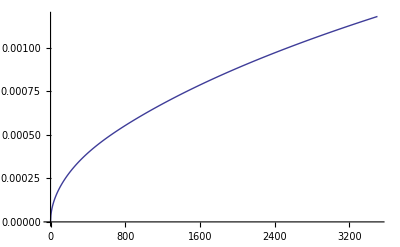

```mathematica
ListPlot[AeTable,PlotJoined-> True]
```

```mathematica
Ae=Interpolation[AeTable]
```

InterpolatingFunction[{{1.×10^-7,3500.}},<>]

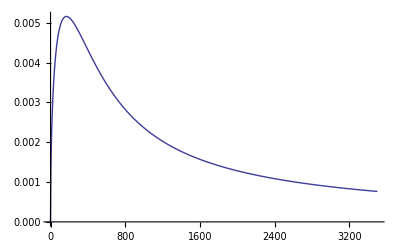

```mathematica
ListPlot[AITable,PlotJoined-> True]
```

```mathematica
AI=Interpolation[AITable]
```

InterpolatingFunction[{{1.×10^-7,3500.}},<>]

```mathematica
SNInt[EE_]:=NIntegrate[(Ae[Ep]+AI[Ep])/(Te*Ae[Ep]+TI*AI[Ep]),{Ep,0,EE}]
```

```mathematica
S=FunctionInterpolation[SNInt[EE],{EE,1.0*10^(-7),3500.0}]
```

NIntegrate::nlim: Ep = EE is not a valid limit of integration.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

InterpolatingFunction[{{1.×10^-7,3500.}},<>]

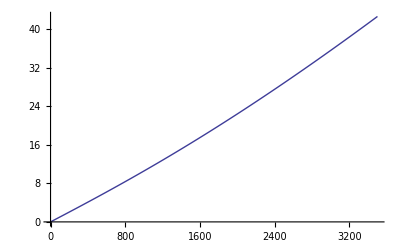

```mathematica
Plot[S[EE],{EE,1.0*10^(-7),3500.0}]
```

```mathematica
hNInt[Ep_]:=NIntegrate[Sqrt[Epp]*Exp[-S[Epp]],{Epp,1.0*10^(-7),Ep}]
```

```mathematica
normalization=hNInt[3500.0]
```

857.815

```mathematica
gTable=Table[{zg,hNInt[zg]/normalization},{zg,1.0*10^(-7),3500.0,1.0}];
```

```mathematica
g=Interpolation[gTable]
```

InterpolatingFunction[{{1.×10^-7,3499.}},<>]

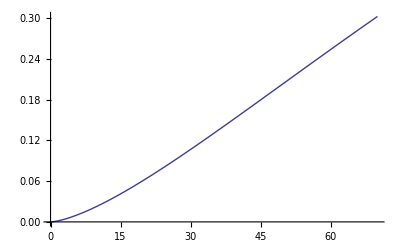

```mathematica
Plot[g[Ep],{Ep,1.0*10^(-7),70}]
```

```mathematica
fNInt[EE_]:=NIntegrate[(Exp[S[Ep]-S[EE]]/Ep/(Te*Ae[Ep]+TI*AI[Ep]))*g[Ep],{Ep,1.0*10^(-7),EE}]
```

```mathematica
fTable=Table[{zf,fNInt[zf]},{zf,1.0*10^(-7),3500.0,1.0}];
```

```mathematica
f=Interpolation[fTable]
```

InterpolatingFunction[{{1.×10^-7,3499.}},<>]

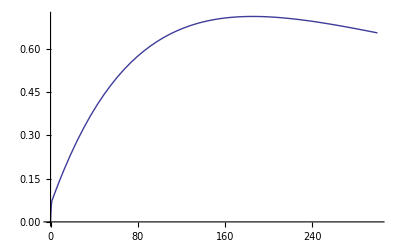

```mathematica
Plot[f[EE],{EE,1.0*10^(-7),300}]
```

```mathematica
f[3000]
```

0.172562

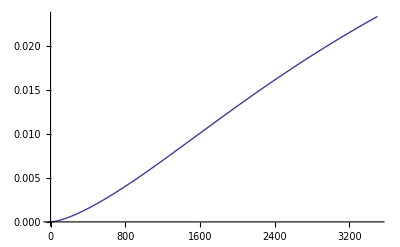

```mathematica
Plot[EE*AI[EE]*Ae[EE]/(TI*AI[EE]+Te*Ae[EE]),{EE,1.0*10^(-7),3500.0}]
```

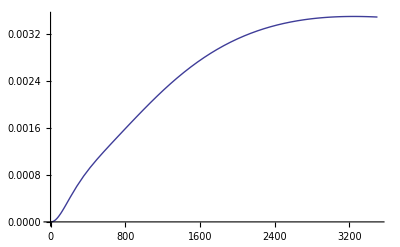

```mathematica
Plot[EE*AI[EE]*Ae[EE]*f[EE]/(TI*AI[EE]+Te*Ae[EE]),{EE,1.0*10^(-7),3500.0}]
```

```mathematica
G3010=NIntegrate[(EE*AI[EE]*Ae[EE]/(TI*AI[EE]+Te*Ae[EE]))*f[EE],{EE,1.0*10^(-7),3499.0}]
```

8.70866

```mathematica
GlossI=((Te-TI)/3500)*(G3010+6.57*f[3500])
Glosse=((TI-Te)/3500)*(G3010+6.57*f[3500])
```

InterpolatingFunction::dmval: Input value {3500} lies outside the range of data in the interpolating function. Extrapolation will be used.

-0.13846

InterpolatingFunction::dmval: Input value {3500} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.13846

```mathematica
Term2lossI=(TI/3500)*NIntegrate[(AI[EE]/(TI*AI[EE]+Te*Ae[EE]))*g[EE],{EE,1.0*10^(-7),3499.0}]
```

0.739397

```mathematica
Term2losse=(Te/3500)*NIntegrate[(Ae[EE]/(TI*AI[EE]+Te*Ae[EE]))*g[EE],{EE,1.0*10^(-7),3499.0}]
```

0.21875

```mathematica
EIoverE0=GlossI+Term2lossI
EeoverE0=Glosse+Term2losse
```

0.600936

0.35721

```mathematica
EbaroverE0=NIntegrate[EE^(3/2)*Exp[-S[EE]],{EE,1.0*10^(-7),3500.0}]/normalization/3500
```

0.0415676

```mathematica
EIoverE0+EeoverE0+EbaroverE0
```

0.999714